## Book Problems

### Chapter 6, Problem 3

```mathematica
DSolve[
{v''[x]+0 v[x]==0,
v'[0]+aL/(1+aL L) v[0]==0,
v'[L]+aL v[L]==0},
v[x],x]//FullSimplify//Expand
```

{{v[x]→-C[1]/aL-L C[1]+x C[1]}}

```mathematica
Reduce[{c1-a0 c2==0&&c1+aL c1 L+aL c2==0&&(c1!=0||c2!=0)}]//FullSimplify
```

a0==c1/c2&&aL+c1/(c2+c1 L)==0

```mathematica
tmp[x_]=C[1] Cos[x √λ]+C[2] Sin[x √λ];
tmp'[L]+aL tmp[x]//FullSimplify
```

aL C[1] Cos[x √λ]+√λ (C[2] Cos[L √λ]-C[1] Sin[L √λ])+aL C[2] Sin[x √λ]

### Chapter 6, Problem 8

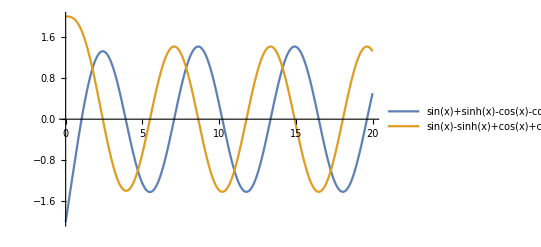

```mathematica
Plot[
{Sin[x]+Sinh[x]-Cos[x]-Cosh[x],
Sin[x]-Sinh[x]+Cos[x]+Cosh[x]
},{x,0,20},
PlotLegends->"Expressions"]
```

```mathematica
Assuming[λ>0&&L>0,
DSolve[
{v''''[x]-μ^4 v[x]==0,
v[0]==0,
v'[0]==0,
v''[L]==0,
v'''[L]==0},
v[x],x
]//FullSimplify]
v1[x_]=a Cos[μ x]+b Sin[μ x]+c Cosh[μ x]+d Sinh[μ x];
v1[0]//FullSimplify
v1'[0]//FullSimplify
v1''[L]/.{c->-a,d->-b}/.{b->-a}//FullSimplify
v1'''[L]/.{c->-a,d->-b}/.{b->-a}//FullSimplify
Assuming[μ!=0&&L>0,v1[0]==0&&v1'[0]==0&&v1''[L]==0&&v1'''[L]==0//FullSimplify]/.{c->-a,d->-b}//FullSimplify
FullSimplify[-a((Cos[L μ]+Cosh[L μ])/(Sin[L μ]+Sinh[L μ]))(Cos[L μ]+Cosh[L μ])+a Sinh[L μ]==a Sin[L μ]]
```

{{v[x]→0}}

a+c

(b+d) μ

a μ^2 (-Cos[L μ]-Cosh[L μ]+Sin[L μ]+Sinh[L μ])

a μ^3 (Cos[L μ]+Cosh[L μ]+Sin[L μ]-Sinh[L μ])

a Cos[L μ]+a Cosh[L μ]+b Sin[L μ]+b Sinh[L μ]==0&&b (Cos[L μ]+Cosh[L μ])+a Sinh[L μ]==a Sin[L μ]

(a+a Cos[L μ] Cosh[L μ])/(Sin[L μ]+Sinh[L μ])==0

```mathematica
Manipulate[Plot[{Cos[x],-Sech[x]},{x,(n-1)π,(n)π}],{n,1,20,1}]
```

```mathematica
Solve[Cos[x]==0,x]
```

{{x→ConditionalExpression[-π/2+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[π/2+2 π C[1], C[1]∈ℤ]}}

```mathematica
DSolve[
{v''[x]+λ v[x]==0},
v[x],x
]//FullSimplify
```

```mathematica
{{v[x]->C[1] Cos[x √λ]+C[2] Sin[x √λ]}}
```

```mathematica
v2[x_]=C[1] Cos[x √λ]+C[2] Sin[x √λ];
v2[0]
```

C[1]

## Additional Problems

### 1

```mathematica
tmp[x_]=u[x]v'[x]-u'[x]v[x];
(tmp[b]-tmp[a])/.
{u[b]->α u[a]+β u'[a],
u'[b]->γ u[a]+δ u'[a],
v[b]->α v[a]+β v'[a],
v'[b]->γ v[a]+δ v'[a]}//FullSimplify
```

(1+β γ-α δ) (v[a] u'[a]-u[a] v'[a])

### 2

```mathematica
DSolve[
{D[(x u'[x]), x]+λ/x u[x]==0,
u[1]==0,
u'[ⅇ]==0},
u[x],
x]//FullSimplify
```

{{u[x]→Piecewise[{{C[1] Sin[√λ Log[x]], (n∈ℤ&&((4 n==1+Abs[1-4 n]&&λ==1/4 (π-4 n π)^2)||(1+4 n==Abs[1+4 n]&&(π+4 n π)^2==4 λ)))||λ==0}, {0, True}}]}}

```mathematica
DSolve[
{v''[x]+λ v[x]==0,
v[0]==0,
v'[1]==0},
v[x],
x]
```

{{v[x]→Piecewise[{{C[1] Sin[x √λ], n∈ℤ&&n≥1&&λ==(-1/2+n)^2 π^2}, {0, True}}]}}

```mathematica
Assuming[n∈Integers&&m∈Integers&&m!=n,∫_1^ⅇ 1/x Sin[(-π/2+n π)Log[x]]Sin[(-π/2+m π)Log[x]]ⅆx//FullSimplify]
```

0

```mathematica
ExpandAll[TrigToExp[Sin[(-π/2+π n)y]Sin[(-π/2+π m)y]]]//FullSimplify
```

Sin[1/2 (1-2 m) π y] Sin[1/2 (1-2 n) π y]

### 3

```mathematica
DSolve[
{D[u[x,t], t]==k D[u[x,t], x,x],
u[x,0]==f[x],
u[1,t]==u[-1,t],
((D[u[x,t], x])/.{x->1})==((D[u[x,t], x])/.{x->-1})},
u[x,t],
{x,t}]
DSolve[
{D[u[x,t], t]==k D[u[x,t], x,x],
u[x,0]==x^2-x^4,
u[1,t]==u[-1,t],
((D[u[x,t], x])/.{x->1})==((D[u[x,t], x])/.{x->-1})},
u[x,t],
{x,t}]
```

{{u[x,t]→Integrate[f[x]/(√2),{x,-1,1},Assumptions→True]/(√2)+ⅇ^(-k π^2 t K[1]^2) (Cos[π x K[1]] Integrate[Cos[π x K[1]] f[x],{x,-1,1},Assumptions→True]+Integrate[f[x] Sin[π x K[1]],{x,-1,1},Assumptions→True] Sin[π x K[1]])K[1]1∞}}

{{u[x,t]→2/15+-(4 (-1)^K[1] ⅇ^(-k π^2 t K[1]^2) Cos[π x K[1]] (-12+π^2 K[1]^2))/(π^4 K[1]^4)K[1]1∞}}

```mathematica
F[x_]=x^2-x^4;
a0=1/2∫_-1^1 F[x]ⅆx//FullSimplify
an[n_]=Assuming[n∈Integers,∫_-1^1 Cos[n π x]F[x]ⅆx//FullSimplify]
bn[n_]=Assuming[n∈Integers,∫_-1^1 Sin[n π x]F[x]ⅆx//FullSimplify]
u1[x_,t_,n_,k_]:=a0+∑_(i=1)^n ⅇ^(-i^2 π^2 k t)(an[i]Cos[i π x]+bn[i]Sin[i π x])
```

2/15

-(4 (-1)^n (-12+n^2 π^2))/(n^4 π^4)

0

```mathematica
Manipulate[
Plot[{u1[x,t,n,1],F[x]},
{x,-1,1},
PlotRange->{{-1,1},{0,1.1/4}}],
{{n,50},0,50,1},{t,0,0.5,0.001}]
```

### 4

```mathematica
tmp[x_,t_]=ϕ[x]ψ[t]+x(Cos[t]-1)+x^2/(2π);
D[tmp[x,t], t,t]
D[tmp[x,t], x,x]
((D[tmp[x,t], x])/.{x->0})==(Cos[t]-1)//FullSimplify
((D[tmp[x,t], x])/.{x->π})==Cos[t]//FullSimplify
tmp[x,0]==x^2/(2π)//FullSimplify
((D[tmp[x,t], t])/.{t->0})==Cos[3x]//FullSimplify
D[tmp[x,t], t,t]-4 D[tmp[x,t], x,x]==(1-x)Cos[t]//Simplify
```

-x Cos[t]+ϕ[x] ψ''[t]

1/π+ψ[t] ϕ''[x]

ψ[t] ϕ'[0]==0

ψ[t] ϕ'[π]==0

ϕ[x] ψ[0]==0

Cos[3 x]==ϕ[x] ψ'[0]

4+π Cos[t]+4 π ψ[t] ϕ''[x]==π ϕ[x] ψ''[t]

```mathematica
DSolve[
{D[u[x,t], t,t]-4 D[u[x,t], x,x]==(1-x)Cos[t],
((D[u[x,t], x])/.x->0)==Cos[t]-1,
((D[u[x,t], x])/.x->π)==Cos[t],
u[x,0]==x^2/(2π),
((D[u[x,t], t])/.t->0)==Cos[3x]},
u[x,t],
{x,t}]//FullSimplify//Expand
```

{{u[x,t]→1+(2 t^2)/π-x+x^2/(2 π)-Cos[t]+x Cos[t]+1/6 Cos[3 x] Sin[6 t]}}

```mathematica
DSolve[
{ψ''[t]==Cos[t]+4/π,
ψ'[0]==0,
ψ[0]==0},
ψ[t],t]//FullSimplify
DSolve[
{ψ''[t]+36ψ[t]==0,
ψ'[0]==1,
ψ[0]==0},
ψ[t],t]//FullSimplify
```

{{ψ[t]→1+(2 t^2)/π-Cos[t]}}

{{ψ[t]→1/6 Sin[6 t]}}

```mathematica
1+(2 t^2)/π-Cos[t]+1/6 Cos[3x]Sin[6t]+x(Cos[t]-1)+x^2/(2π)//FullSimplify//Expand
```

1+(2 t^2)/π-x+x^2/(2 π)-Cos[t]+x Cos[t]+1/6 Cos[3 x] Sin[6 t]

```mathematica
u3[x_,t_]=1+(2 t^2)/π-x+x^2/(2 π)-Cos[t]+x Cos[t]+1/6 Cos[3 x] Sin[6 t];
	∫_0^π ((D[u3[x,t], t])^2+4(D[u3[x,t], x])^2)ⅆx//FullSimplify
```

1/6 π (26+(-3+π) π)+(16 t^2)/π-4 π Cos[t]-1/6 π (-9+(-3+π) π) Cos[2 t]-2/9 (18 (-2+π) t Sin[t]+7 Sin[5 t]-6 Sin[6 t]+5 Sin[7 t])

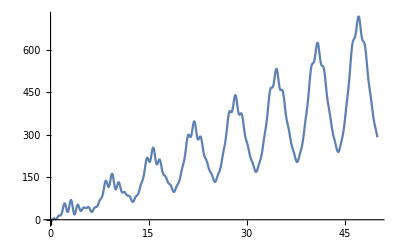

```mathematica
Energy[t_]=1/6 π (26+(-3+π) π)+(16 t^2)/π-4 π Cos[t]-1/6 π (-9+(-3+π) π) Cos[2 t]-2/9 (18 (-2+π) t Sin[t]+7 Sin[5 t]-6 Sin[6 t]+5 Sin[7 t]);
dE[t_]=(32 t)/π-4 (-2+π) t Cos[t]-70/9 Cos[5 t]+8 Cos[6 t]-70/9 Cos[7 t]+8 Sin[t]+1/3 π (-9+(-3+π) π) Sin[2 t];
Plot[dE[t],{t,0,50}]
```

```mathematica
Manipulate[Plot[u3[x,t],{x,0,π},PlotRange->{{0,π},{0,10}}],{t,0,10}]
```